```mathematica
(*This notebook takes around 17 minutes to run in its entirety on my laptop.*)
(*Set notebook directory.*)
SetDirectory[NotebookDirectory[]];

(*Assorted graphics commands.*)
linelegs[label_,legs_,pos_,cols_]:=PlotLegends->Placed[LineLegend[Table[Text[Style[legs[[i]],14,FontFamily->"Times New Roman"]],{i,1,Length[legs]}],LegendLabel->Text[Style[label,14,FontFamily->"Times New Roman"]],LabelStyle->{GrayLevel[0],14},LegendLayout->{"Column",cols}],pos]
frameStyle[xlabel_,ylabel_,fsize_:14]:={Axes->None,Frame->True,FrameStyle->Black,AspectRatio->1/GoldenRatio, FrameLabel->{{Text[Style[ylabel,FontFamily->"Times New Roman",fsize]], Text[Style["",fsize]]}, {Text[Style[xlabel,FontFamily->"Times New Roman",fsize]], Text[Style["",fsize]]}},LabelStyle->{FontFamily->"Times New Roman",fsize}}
text[x0_,y0_,txt_,color_]:=Graphics[Text[Style[txt,color,FontFamily->"Times New Roman",14],{x0,y0}]]
text[x0_,y0_,txt_,color_,size_:fontSize]:=Graphics[Text[Style[txt,color,FontFamily->"Times New Roman",size],{x0,y0}]]
Cell[StyleData["Print"],FontSize->36];

(*Non-universal constants, set to unity for the purposes of these RegionPlots.*)
a=1;
b=1;
ρ=1;
m=1;
(*Expressed in terms of real frequency and wave vector - asymptotically correct form in two spatial dimensions. Limits of integration are where the imaginary part vanishes.*)
(*This is the polarizability - the density-density response before charge is added using RPA. Disorder-smeared with standard deviation Δ.*)
```

```mathematica
AvgImΠnn[ω_,q_,Δ_,δp_]:=NIntegrate[(((ρ^2 a/m^2)q^4 √(b*ω^2*Abs[Log[Abs[dps]]]-dps^2))/(ρ^2 ω^4-2*a*ρ*dps*q^2*ω^2+a^2*b*q^4*ω^2*Abs[Log[Abs[dps]]]))(1/(√(2π)Δ)Exp[-(dps-δp)^2/(2*Δ^2)]),{dps,-Exp[-1/2 ProductLog[0,2/(b*ω^2)]],Exp[-1/2 ProductLog[0,2/(b*ω^2)]]},WorkingPrecision->18];
(*Non-disorder averaged version of above.*)
ImΠnn[ω_,q_,δp_]:=Piecewise[{{((ρ^2 a/m^2)q^4 √(b*ω^2*Abs[Log[Abs[δp]]]-δp^2))/(ρ^2 ω^4-2*a*ρ*δp*q^2*ω^2+a^2*b*q^4*ω^2*Abs[Log[Abs[δp]]]),ω>1/(√b)Abs[δp]/(√Abs[Log[Abs[δp]]])},{0,ω≤ 1/(√b)Abs[δp]/(√Abs[Log[Abs[δp]]])}}];
```

```mathematica
(*These derivatives can be done for the non-disorder-averaged version - logarithmic derivatives give the particular power laws in each region.*)
dlogImΠnndlogω1[logω_,q_,δp_]=D[Log[ImΠnn[Exp[logω],q,δp]],logω];
dlogImΠnndlogq1[ω_,logq_,δp_]=D[Log[ImΠnn[ω,Exp[logq],δp]],logq];
loglogImΠnndω[ω_,q_,δp_]=dlogImΠnndlogω1[Log[ω],q,δp];
loglogImΠnndq[ω_,q_,δp_]=dlogImΠnndlogq1[ω,Log[q],δp];
```

```mathematica
(*Installing MaTeX to make the labels LaTeX font. This sometimes causes my Mathematica to crash.*)
ResourceFunction["MaTeXInstall"][]
<<MaTeX`
```

OpenWrite::noopen: Cannot open C:\Users\steph\AppData\Roaming\Mathematica\Paclets\Repository\MaTeX-1.7.9\Documentation\English\TextSearchIndex\_0.cfs.

BinaryWrite::stream: $Failed is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

General::stop: Further output of BinaryWrite::stream will be suppressed during this calculation.

Close::stream: $Failed is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

Paclet[MaTeX,1.7.9,<>]

```mathematica
(*Test of MaTeX font.*)
MaTeX["-\Pi'' \sim q^{4} \omega^{-3}"]
```

-Graphics-

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

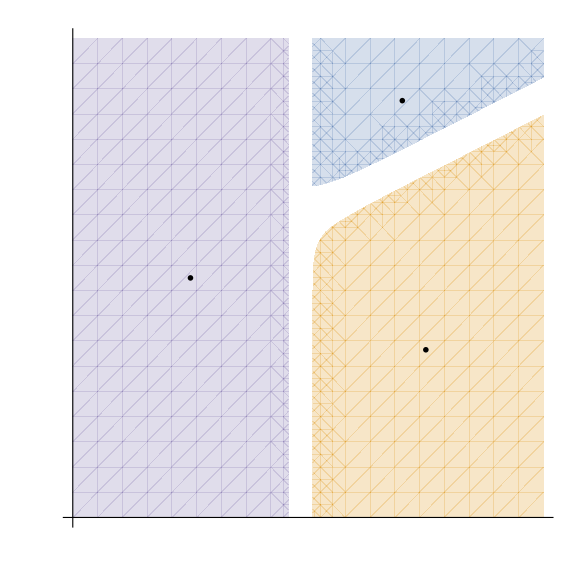

```mathematica
(*Generating region plots for non-disorder-smeared power laws is fast (all of the computation time comes in the careful numerical integration of sharply peaked functions). I know what the power law regions are, so each region is where the logarithmic derivative is within 0.1 of an integer. Power laws in both q and ω are checked, and then labelled as q^α ω^β on the plot.*)
fs=40;
cls=ColorData[97,"ColorList"];
rplota=RegionPlot[{Abs[loglogImΠnndω[Exp[logω],Exp[logq],-10^-3]-(-1)]<0.1&&Abs[loglogImΠnndq[Exp[logω],Exp[logq],-10^-3]-(0)]<0.1},{logω,-8Log[10],2Log[10]},{logq,-8Log[10],2Log[10]},BoundaryStyle->None,PlotStyle->{Opacity[0.25],cls[[1]]}];
rplotb=RegionPlot[{Abs[loglogImΠnndω[Exp[logω],Exp[logq],-10^-3]-(-3)]<0.1&&Abs[loglogImΠnndq[Exp[logω],Exp[logq],-10^-3]-(4)]<0.1},{logω,-8Log[10],2Log[10]},{logq,-8Log[10],2Log[10]},BoundaryStyle->None,PlotStyle->{Opacity[0.25],cls[[2]]}];
rplotc=RegionPlot[{Abs[ImΠnn[Exp[logω],Exp[logq],-10^-3]]==0},{logω,-8Log[10],2Log[10]},{logq,-8Log[10],2Log[10]},BoundaryStyle->None,PlotStyle->{Opacity[0.25],cls[[5]]}];
exp1=text[-0.5Log[10],-4.5Log[10],MaTeX["-\Pi'' \sim q^{4} \omega^{-3}",Magnification->3.5],GrayLevel[0],fs];
exp2=text[-1Log[10],0.7Log[10],MaTeX["\sim q^{0} \omega^{-1}",Magnification->3.5],GrayLevel[0],fs];
exp3=text[-5.5Log[10],-3Log[10],MaTeX["\equiv 0",Magnification->3.5],GrayLevel[0],fs];
ticks={{{Log[10^-7],MaTeX["10^{-7}",Magnification->3.5],{0.03,0}},{Log[10^-5],MaTeX["10^{-5}",Magnification->3.5],{0.03,0}},{Log[10^-3],MaTeX["\omega",Magnification->3.5],{0.03,0}},{Log[10^-1],MaTeX["10^{-1}",Magnification->3.5],{0.03,0}},{Log[10^1],MaTeX["10^{1}",Magnification->3.5],{0.03,0}}},{{Log[10^-7],MaTeX["10^{-7}",Magnification->3.5],{0.03,0}},{Log[10^-5],MaTeX["10^{-5}",Magnification->3.5],{0.03,0}},{Log[10^-3],MaTeX["q\;",Magnification->3.5],{0.03,0}},{Log[10^-1],MaTeX["10^{-1}",Magnification->3.5],{0.03,0}},{Log[10^1],MaTeX["10^{1}",Magnification->3.5],{0.03,0}}}};
Show[rplota,rplotb,rplotc,exp1,exp2,exp3,AspectRatio->1,Frame->False,ImagePadding->{{All,All},{All,All}},Axes->True,Ticks->ticks,TicksStyle->{{Black,Thickness[0.005]},{Black,Thickness[0.005]}},AxesOrigin->{-8Log[10],-8Log[10]},frameStyle["","",fs],ImageSize->Large,PlotLabel->MaTeX["\delta p=-10^{-3}; \; \sigma=0",Magnification->3.5]]
```

```mathematica
(*Non-disorder averaged form for χ in 2D with 3D Coulomb (weakly coupled layers).*)
Imχnn[ω_,q_,e_,δp_]:=Piecewise[{{((ρ^2 a/m^2)q^4 √(b*ω^2*Abs[Log[Abs[δp]]]-δp^2))/((ρ ω^2-a q^2 δp-(4π ρ^2 e^2)/m^2)^2+a^2*b*q^4*ω^2*Abs[Log[Abs[δp]]]-a^2 q^4 δp^2),ω>1/(√b)Abs[δp]/(√Abs[Log[Abs[δp]]])},{0,ω≤ 1/(√b)Abs[δp]/(√Abs[Log[Abs[δp]]])}}];
```

```mathematica
(*Determining power law regions of non-disorder averaged form of χ.*)
dlogImχnndlogω1[logω_,q_,e_,δp_]=D[Log[Imχnn[Exp[logω],q,e,δp]],logω];
dlogImχnndlogq1[ω_,logq_,e_,δp_]=D[Log[Imχnn[ω,Exp[logq],e,δp]],logq];
loglogImχnndω[ω_,q_,e_,δp_]=dlogImχnndlogω1[Log[ω],q,e,δp];
loglogImχnndq[ω_,q_,e_,δp_]=dlogImχnndlogq1[ω,Log[q],e,δp];
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

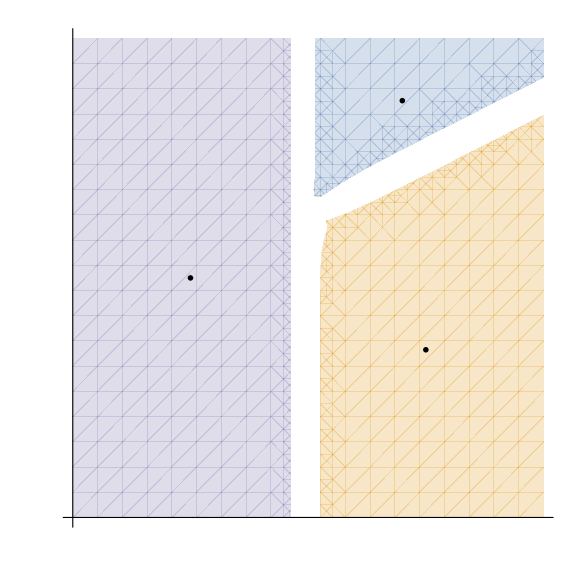

```mathematica
(*Generating figure 2(a). e is set to be 10^-4 so that the remnant of the plasmon bump is located in a similar place to what is seen in the experiment.*)
fs=40;
cls=ColorData[97,"ColorList"];
rplota=RegionPlot[{Abs[loglogImχnndω[Exp[logω],Exp[logq],10^-4,1.1*10^-3]-(-1)]<0.1&&Abs[loglogImχnndq[Exp[logω],Exp[logq],10^-4,1.1*10^-3]-(0)]<0.1},{logω,-8Log[10],2Log[10]},{logq,-8Log[10],2Log[10]},BoundaryStyle->None,PlotStyle->{Opacity[0.25],cls[[1]]}];
rplotb=RegionPlot[{Abs[loglogImχnndω[Exp[logω],Exp[logq],10^-4,1.1*10^-3]-(-3)]<0.1&&Abs[loglogImχnndq[Exp[logω],Exp[logq],10^-4,1.1*10^-3]-(4)]<0.1},{logω,-8Log[10],2Log[10]},{logq,-8Log[10],2Log[10]},BoundaryStyle->None,PlotStyle->{Opacity[0.25],cls[[2]]}];
rplotc=RegionPlot[{Abs[Imχnn[Exp[logω],Exp[logq],10^-4,1.1*10^-3]]==0},{logω,-8Log[10],2Log[10]},{logq,-8Log[10],2Log[10]},BoundaryStyle->None,PlotStyle->{Opacity[0.25],cls[[5]]}];
exp1=text[-0.5Log[10],-4.5Log[10],MaTeX["-\chi'' \sim q^{4} \omega^{-3}",Magnification->3.5],GrayLevel[0],fs];
exp2=text[-1Log[10],0.7Log[10],MaTeX["\sim q^{0} \omega^{-1}",Magnification->3.5],GrayLevel[0],fs];
exp3=text[-5.5Log[10],-3Log[10],MaTeX["\equiv 0",Magnification->3.5],GrayLevel[0],fs];
ticks={{{Log[10^-7],MaTeX["10^{-7}",Magnification->3.5],{0.03,0}},{Log[10^-5],MaTeX["10^{-5}",Magnification->3.5],{0.03,0}},{Log[10^-3],MaTeX["\omega",Magnification->3.5],{0.03,0}},{Log[10^-1],MaTeX["10^{-1}",Magnification->3.5],{0.03,0}},{Log[10^1],MaTeX["10^{1}",Magnification->3.5],{0.03,0}}},{{Log[10^-7],MaTeX["10^{-7}",Magnification->3.5],{0.03,0}},{Log[10^-5],MaTeX["10^{-5}",Magnification->3.5],{0.03,0}},{Log[10^-3],MaTeX["q\;",Magnification->3.5],{0.03,0}},{Log[10^-1],MaTeX["10^{-1}",Magnification->3.5],{0.03,0}},{Log[10^1],MaTeX["10^{1}",Magnification->3.5],{0.03,0}}}};
fig2a=Show[rplota,rplotb,rplotc,exp1,exp2,exp3,AspectRatio->1,Frame->False,ImagePadding->{{All,All},{All,All}},Axes->True,Ticks->ticks,TicksStyle->{{Black,Thickness[0.005]},{Black,Thickness[0.005]}},AxesOrigin->{-8Log[10],-8Log[10]},frameStyle["","",fs],ImageSize->Large,PlotLabel->MaTeX["\delta p=1.1 \\times 10^{-3}; \; \sigma=0",Magnification->3.5]]
```

```mathematica
(*Disorder-smeared version of χ.*)
AvgImχnn[ω_,q_,e_,Δ_,δp_]:=NIntegrate[(((ρ^2 a/m^2)q^4 √(b*ω^2*Abs[Log[Abs[dps]]]-dps^2))/((ρ ω^2-a q^2 dps-(4π ρ^2 e^2)/m^2)^2+a^2*b*q^4*ω^2*Abs[Log[Abs[dps]]]-a^2 q^4 dps^2))(1/(√(2π)Δ)Exp[-(dps-δp)^2/(2*Δ^2)]),{dps,-Exp[-1/2 ProductLog[0,2/(b*ω^2)]],Exp[-1/2 ProductLog[0,2/(b*ω^2)]]},WorkingPrecision->18];
```

```mathematica
Quiet[
dlogAvgImχnndlogω1[logω_,q_,e_,Δ_,δp_]=D[Log[AvgImχnn[Exp[logω],q,e,Δ,δp]],logω];
dlogAvgImχnndlogq1[ω_,logq_,e_,Δ_,δp_]=D[Log[AvgImχnn[ω,Exp[logq],e,Δ,δp]],logq];
loglogAvgImχnndω[ω_,q_,e_,Δ_,δp_]=dlogAvgImχnndlogω1[Log[ω],q,e,Δ,δp];
loglogAvgImχnndq[ω_,q_,e_,Δ_,δp_]=dlogAvgImχnndlogq1[ω,Log[q],e,Δ,δp];
]
```

NIntegrate::precw: The precision of the argument function ((443.269 ⅇ^(-617284. (-0.0011+dps)^2+4 logq) √(-dps^2+ⅇ^(2 logω) Abs[Log[Abs[dps]]]))/(-dps^2 ⅇ^(4 logq)+(-dps ⅇ^Times[«2»]+ⅇ^(2 logω)-π/25000000)^2+ⅇ^(4 logq+2 logω) Abs[Log[Abs[dps]]])) is less than WorkingPrecision (18.).

NIntegrate::nlim: dps = -1. 2.71828182845904524^(-0.5 ProductLog[2. 2.71828182845904524^(-2. logω)]) is not a valid limit of integration.

NIntegrate::precw: The precision of the argument function (443.269 ⅇ^(-617284. (-0.0011+dps)^2) ((ⅇ^(4 logq+2 logω) Abs[Log[Abs[dps]]])/(√(-dps^2+ⅇ^Times[«2»] Abs[Log[«1»]]) (-dps^2 ⅇ^Times[«2»]+(Times[«3»]+Power[«2»]+Times[«2»])^2+ⅇ^Plus[«2»] Abs[Log[«1»]]))-(ⅇ^(4 logq) √(-dps^2+ⅇ^Times[«2»] Abs[Log[«1»]]) (4 ⅇ^(2 logω) (-dps Power[«2»]+ⅇ^Times[«2»]-π/25000000)+2 ⅇ^(Times[«2»]+Times[«2»]) Abs[Log[Abs[«1»]]]))/((-dps^2 ⅇ^Times[«2»]+(Times[«3»]+Power[«2»]+Times[«2»])^2+ⅇ^Plus[«2»] Abs[Log[«1»]])^2))) is less than WorkingPrecision (18.).

NIntegrate::nlim: dps = -1. 2.71828182845904524^(-0.5 ProductLog[2. 2.71828182845904524^(-2. logω)]) is not a valid limit of integration.

NIntegrate::precw: The precision of the argument function ((443.269 ⅇ^(-617284. (-0.0011+dps)^2+4 logq) √(-dps^2+ⅇ^(2 logω) Abs[Log[Abs[dps]]]))/(-dps^2 ⅇ^(4 logq)+(-dps ⅇ^Times[«2»]+ⅇ^(2 logω)-π/25000000)^2+ⅇ^(4 logq+2 logω) Abs[Log[Abs[dps]]])) is less than WorkingPrecision (18.).

General::stop: Further output of NIntegrate::precw will be suppressed during this calculation.

NIntegrate::nlim: dps = -1. 2.71828182845904524^(-0.5 ProductLog[2. 2.71828182845904524^(-2. logω)]) is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

General::munfl: Exp[-2371.94] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2543.2] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2371.94] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NIntegrate::precw: The precision of the argument function ((443.269 ⅇ^(-617284. (-0.0011+dps)^2+4 logq) √(-dps^2+ⅇ^(2 logω) Abs[Log[Abs[dps]]]))/(-dps^2 ⅇ^(4 logq)+(-dps ⅇ^Times[«2»]+ⅇ^(2 logω)-π/25000000)^2+ⅇ^(4 logq+2 logω) Abs[Log[Abs[dps]]])) is less than WorkingPrecision (18.).

NIntegrate::nlim: dps = -1. 2.71828182845904524^(-0.5 ProductLog[2. 2.71828182845904524^(-2. logω)]) is not a valid limit of integration.

NIntegrate::precw: The precision of the argument function (443.269 ⅇ^(-617284. (-0.0011+dps)^2) ((ⅇ^(4 logq+2 logω) Abs[Log[Abs[dps]]])/(√(-dps^2+ⅇ^Times[«2»] Abs[Log[«1»]]) (-dps^2 ⅇ^Times[«2»]+(Times[«3»]+Power[«2»]+Times[«2»])^2+ⅇ^Plus[«2»] Abs[Log[«1»]]))-(ⅇ^(4 logq) √(-dps^2+ⅇ^Times[«2»] Abs[Log[«1»]]) (4 ⅇ^(2 logω) (-dps Power[«2»]+ⅇ^Times[«2»]-π/25000000)+2 ⅇ^(Times[«2»]+Times[«2»]) Abs[Log[Abs[«1»]]]))/((-dps^2 ⅇ^Times[«2»]+(Times[«3»]+Power[«2»]+Times[«2»])^2+ⅇ^Plus[«2»] Abs[Log[«1»]])^2))) is less than WorkingPrecision (18.).

NIntegrate::nlim: dps = -1. 2.71828182845904524^(-0.5 ProductLog[2. 2.71828182845904524^(-2. logω)]) is not a valid limit of integration.

NIntegrate::precw: The precision of the argument function ((443.269 ⅇ^(-617284. (-0.0011+dps)^2+4 logq) √(-dps^2+ⅇ^(2 logω) Abs[Log[Abs[dps]]]))/(-dps^2 ⅇ^(4 logq)+(-dps ⅇ^Times[«2»]+ⅇ^(2 logω)-π/25000000)^2+ⅇ^(4 logq+2 logω) Abs[Log[Abs[dps]]])) is less than WorkingPrecision (18.).

General::stop: Further output of NIntegrate::precw will be suppressed during this calculation.

NIntegrate::nlim: dps = -1. 2.71828182845904524^(-0.5 ProductLog[2. 2.71828182845904524^(-2. logω)]) is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

General::munfl: Exp[-2371.94] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2543.2] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-17550.2] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NIntegrate::precw: The precision of the argument function ((443.269 ⅇ^(-617284. (-0.0011+dps)^2+4 logq) √(-dps^2+ⅇ^(2 logω) Abs[Log[Abs[dps]]]))/(-dps^2 ⅇ^(4 logq)+(-dps ⅇ^Times[«2»]+ⅇ^(2 logω)-π/25000000)^2+ⅇ^(4 logq+2 logω) Abs[Log[Abs[dps]]])) is less than WorkingPrecision (18.).

NIntegrate::nlim: dps = -1. 2.71828182845904524^(-0.5 ProductLog[2. 2.71828182845904524^(-2. logω)]) is not a valid limit of integration.

NIntegrate::precw: The precision of the argument function (443.269 ⅇ^(-617284. (-0.0011+dps)^2) ((ⅇ^(4 logq+2 logω) Abs[Log[Abs[dps]]])/(√(-dps^2+ⅇ^Times[«2»] Abs[Log[«1»]]) (-dps^2 ⅇ^Times[«2»]+(Times[«3»]+Power[«2»]+Times[«2»])^2+ⅇ^Plus[«2»] Abs[Log[«1»]]))-(ⅇ^(4 logq) √(-dps^2+ⅇ^Times[«2»] Abs[Log[«1»]]) (4 ⅇ^(2 logω) (-dps Power[«2»]+ⅇ^Times[«2»]-π/25000000)+2 ⅇ^(Times[«2»]+Times[«2»]) Abs[Log[Abs[«1»]]]))/((-dps^2 ⅇ^Times[«2»]+(Times[«3»]+Power[«2»]+Times[«2»])^2+ⅇ^Plus[«2»] Abs[Log[«1»]])^2))) is less than WorkingPrecision (18.).

NIntegrate::nlim: dps = -1. 2.71828182845904524^(-0.5 ProductLog[2. 2.71828182845904524^(-2. logω)]) is not a valid limit of integration.

NIntegrate::precw: The precision of the argument function ((443.269 ⅇ^(-617284. (-0.0011+dps)^2+4 logq) √(-dps^2+ⅇ^(2 logω) Abs[Log[Abs[dps]]]))/(-dps^2 ⅇ^(4 logq)+(-dps ⅇ^Times[«2»]+ⅇ^(2 logω)-π/25000000)^2+ⅇ^(4 logq+2 logω) Abs[Log[Abs[dps]]])) is less than WorkingPrecision (18.).

General::stop: Further output of NIntegrate::precw will be suppressed during this calculation.

NIntegrate::nlim: dps = -1. 2.71828182845904524^(-0.5 ProductLog[2. 2.71828182845904524^(-2. logω)]) is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in dps near {dps} = {-0.000080932318402857092504812431879471163024351163426582104629861190599283}. NIntegrate obtained 466.45540752169971702000561501446414185683728514017666771468997684244-0.0030250407216096413840715228758452813140975566704429393028876582060253 ⅈ and 0.0046589899538790955195146956778982091159596038095210398552582222907203 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in dps near {dps} = {-0.000025521015728491960361283207476159189323929453322527358204886183469312}. NIntegrate obtained -3.4172113135140338603559257813628059595490095717484042867700439458612 and 2.2239994871805364211782416762017432496671007673291219227561194499995×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in dps near {dps} = {-0.00025482984479425963486303027010513903841387683140406798600622657231396}. NIntegrate obtained 0.53117624446627975074228357489760890381833509628177574716547865210724-2.9034925827986759894630419090587937418494463838400116200508562961116×10^-6 ⅈ and 4.3584560504785916972363040280259773452087491297724011022320488713356×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::precw: The precision of the argument function ((443.269 ⅇ^(-617284. (-0.0011+dps)^2+4 logq) √(-dps^2+ⅇ^(2 logω) Abs[Log[Abs[dps]]]))/(-dps^2 ⅇ^(4 logq)+(-dps ⅇ^Times[«2»]+ⅇ^(2 logω)-π/25000000)^2+ⅇ^(4 logq+2 logω) Abs[Log[Abs[dps]]])) is less than WorkingPrecision (18.).

NIntegrate::nlim: dps = -1. 2.71828182845904524^(-0.5 ProductLog[2. 2.71828182845904524^(-2. logω)]) is not a valid limit of integration.

NIntegrate::precw: The precision of the argument function (443.269 ⅇ^(-617284. (-0.0011+dps)^2) ((ⅇ^(4 logq+2 logω) Abs[Log[Abs[dps]]])/(√(-dps^2+ⅇ^Times[«2»] Abs[Log[«1»]]) (-dps^2 ⅇ^Times[«2»]+(Times[«3»]+Power[«2»]+Times[«2»])^2+ⅇ^Plus[«2»] Abs[Log[«1»]]))-(ⅇ^(4 logq) √(-dps^2+ⅇ^Times[«2»] Abs[Log[«1»]]) (4 ⅇ^(2 logω) (-dps Power[«2»]+ⅇ^Times[«2»]-π/25000000)+2 ⅇ^(Times[«2»]+Times[«2»]) Abs[Log[Abs[«1»]]]))/((-dps^2 ⅇ^Times[«2»]+(Times[«3»]+Power[«2»]+Times[«2»])^2+ⅇ^Plus[«2»] Abs[Log[«1»]])^2))) is less than WorkingPrecision (18.).

NIntegrate::nlim: dps = -1. 2.71828182845904524^(-0.5 ProductLog[2. 2.71828182845904524^(-2. logω)]) is not a valid limit of integration.

NIntegrate::precw: The precision of the argument function ((443.269 ⅇ^(-617284. (-0.0011+dps)^2+4 logq) √(-dps^2+ⅇ^(2 logω) Abs[Log[Abs[dps]]]))/(-dps^2 ⅇ^(4 logq)+(-dps ⅇ^Times[«2»]+ⅇ^(2 logω)-π/25000000)^2+ⅇ^(4 logq+2 logω) Abs[Log[Abs[dps]]])) is less than WorkingPrecision (18.).

General::stop: Further output of NIntegrate::precw will be suppressed during this calculation.

NIntegrate::nlim: dps = -1. 2.71828182845904524^(-0.5 ProductLog[2. 2.71828182845904524^(-2. logω)]) is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in dps near {dps} = {-0.000080932318402857078649866975616039967490286052126863416717624271455948}. NIntegrate obtained 4.5890474867729663014383982755078987544595803865738399488947665512501-8.4227344630920215835626986185191113525101033684508116115621427164706×10^-8 ⅈ and 8.0468084030211632009711074983338913697758097205233089506806120410561×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in dps near {dps} = {-0.000080932318402857092504812431879471163024351163426582104629861190599283}. NIntegrate obtained 466.45540752169971702000561501446414185683728514017666771468997684244-0.0030250407216096413840715228758452813140975566704429393028876582060253 ⅈ and 0.0046589899538790955195146956778982091159596038095210398552582222907203 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in dps near {dps} = {-2.496939045509039596957179400680804616505198340244318868568220926366×10^-6}. NIntegrate obtained 68.123984025334266427989239791041705723268236764086409663726908535626-7.5285969980081790252408673446893049362487822450998768060276089197202×10^-7 ⅈ and 1.1276251659643358691983239843886329780492901955349936988391335422067×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

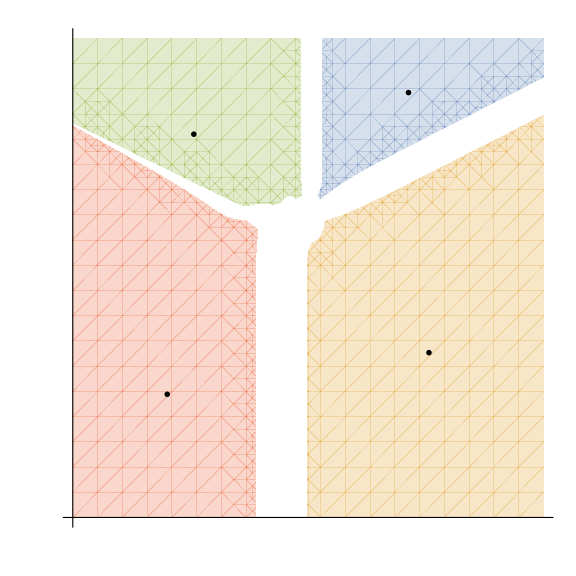

```mathematica
(*Generating Figure 2(b) - this takes the bulk of the time ~16 minutes.*)
fs=40;
cls=ColorData[97,"ColorList"];
rplota=RegionPlot[{Abs[loglogAvgImχnndω[Exp[logω],Exp[logq],10^-4,0.9*10^-3,1.1*10^-3]-(-1)]<0.1&&Abs[loglogAvgImχnndq[Exp[logω],Exp[logq],10^-4,0.9*10^-3,1.1*10^-3]-(0)]<0.1},{logω,-8Log[10],2Log[10]},{logq,-8Log[10],2Log[10]},BoundaryStyle->None,PlotStyle->{Opacity[0.25],cls[[1]]},"NumericalFunction"->False];
rplotb=RegionPlot[{Abs[loglogAvgImχnndω[Exp[logω],Exp[logq],10^-4,0.9*10^-3,1.1*10^-3]-(-3)]<0.1&&Abs[loglogAvgImχnndq[Exp[logω],Exp[logq],10^-4,0.9*10^-3,1.1*10^-3]-(4)]<0.1},{logω,-8Log[10],2Log[10]},{logq,-8Log[10],2Log[10]},BoundaryStyle->None,PlotStyle->{Opacity[0.25],cls[[2]]},"NumericalFunction"->False];
rplotc=RegionPlot[{Abs[loglogAvgImχnndω[Exp[logω],Exp[logq],10^-4,0.9*10^-3,1.1*10^-3]-(0)]<0.1&&Abs[loglogAvgImχnndq[Exp[logω],Exp[logq],10^-4,0.9*10^-3,1.1*10^-3]-(0)]<0.1},{logω,-8Log[10],2Log[10]},{logq,-8Log[10],2Log[10]},BoundaryStyle->None,PlotStyle->{Opacity[0.25],cls[[3]]},"NumericalFunction"->False];
rplotd=RegionPlot[{Abs[loglogAvgImχnndω[Exp[logω],Exp[logq],10^-4,0.9*10^-3,1.1*10^-3]-(2)]<0.1&&Abs[loglogAvgImχnndq[Exp[logω],Exp[logq],10^-4,0.9*10^-3,1.1*10^-3]-(4)]<0.1},{logω,-8Log[10],2Log[10]},{logq,-8Log[10],2Log[10]},BoundaryStyle->None,PlotStyle->{Opacity[0.25],cls[[4]]},"NumericalFunction"->False];
exp1=text[-1.0,-10.5,MaTeX["-\chi'' \sim q^{4} \omega^{-3}",Magnification->3.5],GrayLevel[0],fs];
exp2=text[-2,2,MaTeX["\sim q^{0} \omega^{-1}",Magnification->3.5],GrayLevel[0],fs];
exp3=text[-12.5,0,MaTeX["\sim q^{0} \omega^{0}",Magnification->3.5],GrayLevel[0],fs];
exp4=text[-13.8,-12.5,MaTeX["\sim q^{4} \omega^{2}",Magnification->3.5],GrayLevel[0],fs];
ticks={{{Log[10^-7],MaTeX["10^{-7}",Magnification->3.5],{0.03,0}},{Log[10^-5],MaTeX["10^{-5}",Magnification->3.5],{0.03,0}},{Log[10^-3],MaTeX["\omega",Magnification->3.5],{0.03,0}},{Log[10^-1],MaTeX["10^{-1}",Magnification->3.5],{0.03,0}},{Log[10^1],MaTeX["10^{1}",Magnification->3.5],{0.03,0}}},{{Log[10^-7],MaTeX["10^{-7}",Magnification->3.5],{0.03,0}},{Log[10^-5],MaTeX["10^{-5}",Magnification->3.5],{0.03,0}},{Log[10^-3],MaTeX["q\;",Magnification->3.5],{0.03,0}},{Log[10^-1],MaTeX["10^{-1}",Magnification->3.5],{0.03,0}},{Log[10^1],MaTeX["10^{1}",Magnification->3.5],{0.03,0}}}};
fig2b=Show[rplota,rplotb,rplotc,rplotd,exp1,exp2,exp3,exp4,AspectRatio->1,Frame->False,ImagePadding->{{All,All},{All,All}},Axes->True,Ticks->ticks,TicksStyle->{{Black,Thickness[0.005]},{Black,Thickness[0.005]}},AxesOrigin->{-8Log[10],-8Log[10]},frameStyle["","",fs],ImageSize->Large,PlotLabel->MaTeX["\delta p=1.1 \\times 10^{-3}; \; \sigma=0.9 \\times 10^{-3}",Magnification->3.5]]
```

```mathematica
(*Figure labels.*)
atext=Show[MaTeX["\mathrm{(a)}",Magnification->5.5],ImagePadding->{{0,0},{0,0}}];
btext=Show[MaTeX["\mathrm{(b)}",Magnification->5.5],ImagePadding->{{0,0},{0,0}}];
```

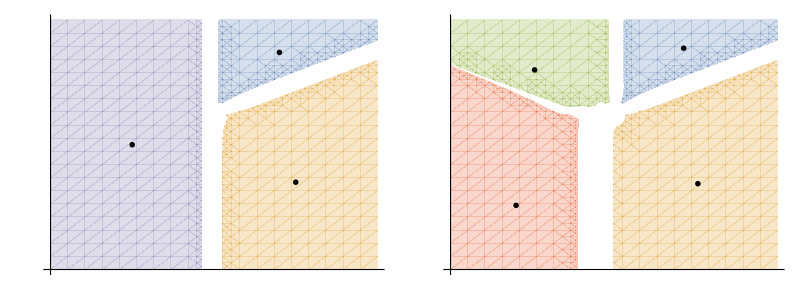

```mathematica
(*Figure 2, after labels and graphs are manually resized wrt one another.*)
Grid[{{atext,btext},{fig2a,fig2b}},Spacings->{0,0}]
```